# 1 DOF

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Universita\MAGISTRALE\MasterThesis\Mathematica

```mathematica
scientstring[n_,dig_]:=ToString[ScientificForm[n,dig],TraditionalForm]
```

```mathematica
GetStep[vec_]:=Mean@Differences[vec]
```

```mathematica
LinSpace[s_,f_,n_]:=Range[s,f,(f-s)/(n-1)]
```

```mathematica
colors={Blue,Red,Green};
```

```mathematica
opts={GridLines->Automatic,LabelStyle->{Black,Bold,FontFamily->"Times New Roman",FontSize->12},AxesStyle->{FontFamily->"Times New Roman"},Frame->True};
```

## Data and Model

```mathematica
alldata=Import["data.m"]
```

<|cellVal→{ν→0.3,Yp→2.5×10^9,ϵp→3.009×10^-11,ϵf→2.3895×10^-11,EBDp→303000000,EBDf→1.574×10^8,l0→1/40,w0→1/10,tp0→1/40000,tf0→1/100000,ξ0→3/1000,ϵ1max→0.05},tankVal→{d→5,Pt→50000,Vtank→1,Vftot→1,f→0.1},gasVal→{patm→101325,Tstd→288.15,gammaair→1.4,rhostdair→1.225,cv→717.2,cp→1.0042}|>

```mathematica
celldata=alldata["cellVal"]//N
```

{ν→0.3,Yp→2.5×10^9,ϵp→3.009×10^-11,ϵf→2.3895×10^-11,EBDp→3.03×10^8,EBDf→1.574×10^8,l0→0.025,w0→0.1,tp0→0.000025,tf0→0.00001,ξ0→0.003,ϵ1max→0.05}

```mathematica
Δtf=dtf/.Solve[((x-tf0)/2)/l0==(dtf/2)/(l0-(ξ-ξ0)),dtf][[1]]
```

-((tf0-x) (l0-ξ+ξ0))/l0

```mathematica
tf=tf0+Δtf;
```

```mathematica
pstraincond={ϵ1[x]->-1+√(1+((x-tf0)/(2 l0))^2),ϵ2[x]->0,ϵ3[x]->ϵ1[x] ν/(ν-1),σ1[x]->-Yp ϵ1[x]/(ν^2-1),σ2[x]->-Yp ν ϵ1[x]/(ν^2-1)};
pstresscond={ϵ1[x]->-1+√(1+((x-tf0)/(2 l0))^2),ϵ2[x]->-ϵ1[x] ν,ϵ3[x]->-ϵ1[x] ν,σ1[x]->Yp ϵ1[x]};
nostraincond={ϵ1[x]->0,ϵ2[x]->0,ϵ3[x]->0,σ1[x]->0,σ2[x]->0,σ3[x]->0};
```

```mathematica
computegeometry1[tf_]:=Module[{ltmp,tptmp,wtmp,Atmp,dAtmp,dCptmp,dCftmp,dCtmp,Ctmp,Volptmp,Volftmp,Voltmp},
ltmp=l0 (1+ϵ1[x]);
tptmp=tp0(1+ϵ3[x]);
wtmp=w0(1+ϵ2[x]);
Atmp=ltmp wtmp;
dAtmp=wtmp(1+ϵ1[x]);
dCptmp=(dAtmp ϵp)/tptmp;
dCftmp=(dAtmp ϵf)/tf;
dCtmp=(2/dCptmp+1/dCftmp)^(-1);
Ctmp=Integrate[dCtmp,ξ];
Ctmp=(Ctmp/. ξ->ξ0+l0)-(Ctmp/. ξ->ξ0)//Simplify;
Volptmp=2wtmp tptmp ltmp;
Volftmp=wtmp(2((x-tf0)/2 √(ltmp^2-((x-tf0)/2)^2))/2+ x ξ0);(*+tf0 √(ltmp^2-((x-tf0)/2)^2));*)
Voltmp=Volptmp+Volftmp;
{l->ltmp,tp->tptmp,w->wtmp,A->Atmp,dA->dAtmp,dCp->dCptmp,dCf->dCftmp,dC->dCtmp,CC->Ctmp,Volp->Volptmp,Volf->Volftmp,Vol->Voltmp}
]
```

```mathematica
geometry=computegeometry1[tf];
```

```mathematica
pstrain=Union[computegeometry1[tf]//.pstraincond,pstraincond];
pstress=Union[computegeometry1[tf]//.pstresscond,pstresscond];
nostrain=Union[computegeometry1[tf]//.nostraincond,nostraincond];
```

```mathematica
tolxmin=10^-10;
xmin=tf0+tolxmin/.celldata//N
xmaxth=x/.Solve[x>0&&((ϵ1[x]/.pstraincond)==ϵ1max)/.celldata,x][[1]]
```

0.0000100001

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.0160178

```mathematica
w0range=w0{0.5,1,1.5}/.celldata;
tp0range=tp0{0.5,1,1.5}/.celldata;
l0range=l0{0.5,1,1.5}/.celldata;
ξ0l0ratio=ξ0/l0/.celldata;
ξ0range=l0range ξ0l0ratio;
```

```mathematica
l0strings=Table[StringJoin["l_0 = " ,scientstring[l0range[[i]],3]," [m]"],{i,1,Length@l0range}];
tp0strings=Table[StringJoin["tp_0 = " ,scientstring[tp0range[[i]],3]," [m]"],{i,1,Length@tp0range}];
w0strings=Table[StringJoin["w_0 = " ,scientstring[w0range[[i]],3]," [m]"],{i,1,Length@w0range}];
ξ0strings=Table[StringJoin["ξ_0 = " ,scientstring[ξ0range[[i]],3],"[m]"],{i,1,Length@ξ0range}];
defstrings={"Plane strain","Plane stress","No strain"};
```

## Analysis

### Capacitance

```mathematica
Capac=CC/.pstrain
```

(l0 w0 √(1+(-tf0+x)^2/(4 l0^2)) ϵf (Log[l0 (2 tp0 ϵf+tf0 ϵp+(2 tp0 (-1+√(1+(-tf0+x)^2/(4 l0^2))) ϵf ν)/(-1+ν))]-Log[l0 (2 tp0 ϵf+x ϵp+(2 tp0 (-1+√(1+(-tf0+x)^2/(4 l0^2))) ϵf ν)/(-1+ν))]))/(tf0-x)

#### Different Deformations

```mathematica
Cdef={Capac/.pstrain,Capac/.pstress,Capac/.nostrain}/.celldata;
```

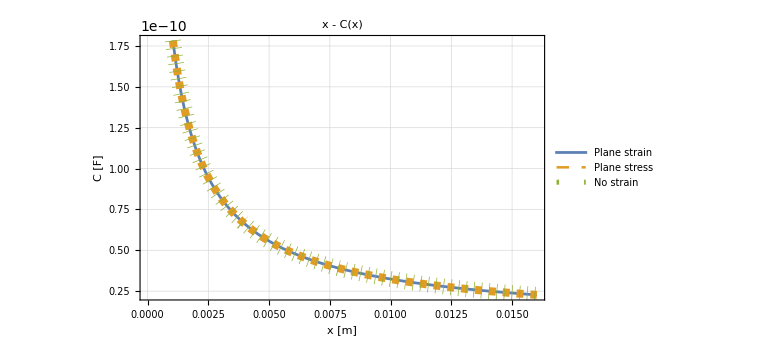

```mathematica
Plot[Cdef,{x,xmin,xmaxth},PlotStyle->{Automatic,{Dashed,Thickness@0.01},{Dotted,Thickness@0.02}},Evaluate@opts,FrameLabel->{"x [m]","C [F]"},PlotLabel->"x - C(x)",PlotLegends->defstrings,ImageSize->Large]
```

#### Geometry variation

```mathematica
Cl0=Capac/.l0->l0range/.celldata//Simplify;
Cw0=Capac/.w0->w0range/.celldata//Simplify;
Ctp0=Capac/.tp0->tp0range/.celldata//Simplify;
```

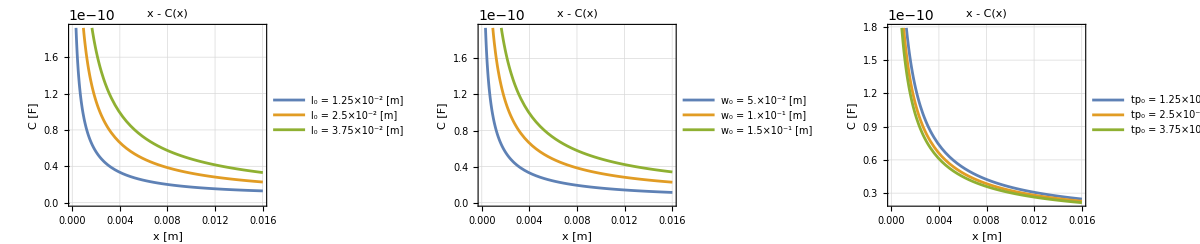

```mathematica
GraphicsRow[{
Plot[Cl0,{x,xmin,xmaxth},Evaluate@opts,FrameLabel->{"x [m]","C [F]"},PlotLabel->"x - C(x)",PlotLegends->{Placed[l0strings,{Center,Right}]}],
Plot[Cw0,{x,xmin,xmaxth},Evaluate@opts,FrameLabel->{"x [m]","C [F]"},PlotLabel->"x - C(x)",PlotLegends->{Placed[w0strings,{Center,Right}]}],
Plot[Ctp0,{x,xmin,xmaxth},Evaluate@opts,FrameLabel->{"x [m]","C [F]"},PlotLabel->"x - C(x)",PlotLegends->{Placed[tp0strings,{Center,Right}]}]
},ImageSize->Full]
```

### Max Voltage

```mathematica
Vmax=2 tp/ϵp Min[ϵp EBDp,ϵf EBDf]//Simplify;
```

#### Different deformation

```mathematica
Vmaxpepssig={Vmax//.pstrain,Vmax//.pstress}/.celldata;
```

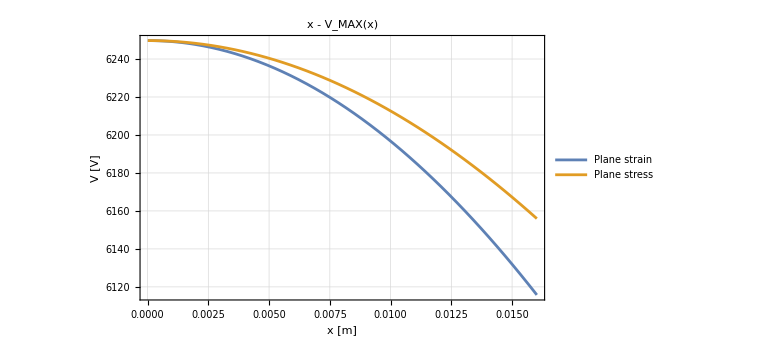

```mathematica
Plot[Vmaxpepssig,{x,xmin,xmaxth},Evaluate@opts,ImageSize->Large,FrameLabel->{"x [m]","V [V]"},PlotLabel->"x - V_MAX(x)",PlotLegends->defstrings]
```

#### l0 variation - Plane strain

```mathematica
Vmaxl0=Vmax/.pstrain/.l0->l0range/.celldata
```

{6249.71 (1-0.428571 (-1+√(1+1600. (-0.00001+x)^2))),6249.71 (1-0.428571 (-1+√(1+400. (-0.00001+x)^2))),6249.71 (1-0.428571 (-1+√(1+177.778 (-0.00001+x)^2)))}

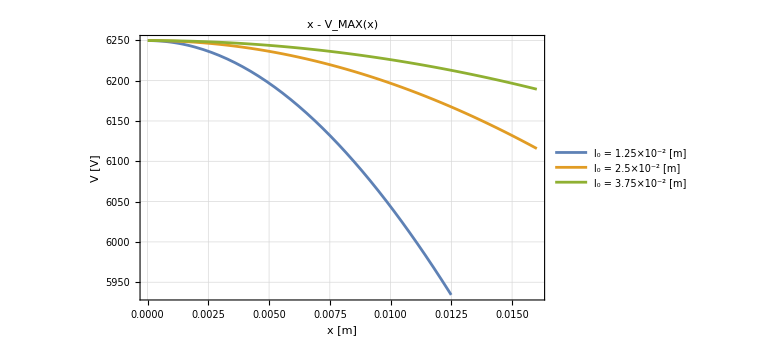

```mathematica
Plot[Vmaxl0,{x,xmin,xmaxth},Evaluate@opts,ImageSize->Large,FrameLabel->{"x [m]","V [V]"},PlotLabel->"x - V_MAX(x)",PlotLegends->l0strings]
```

### Pure elastic energy

```mathematica
pureUel=1/2 σ1[x] ϵ1[x] w tp l;
pureUelx={pureUel//.pstrain,pureUel//.pstress}/.celldata
```

{85.8516 (1-0.428571 (-1+√(1+400. (-0.00001+x)^2))) (-1+√(1+400. (-0.00001+x)^2))^2 √(1+400. (-0.00001+x)^2),78.125 (1-0.3 (-1+√(1+400. (-0.00001+x)^2)))^2 (-1+√(1+400. (-0.00001+x)^2))^2 √(1+400. (-0.00001+x)^2)}

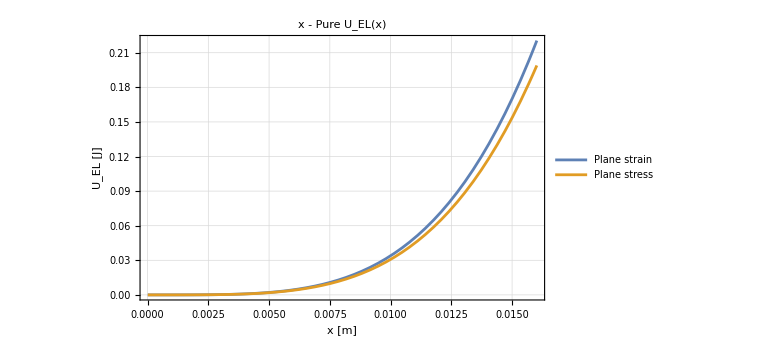

```mathematica
Plot[pureUelx,{x,xmin,xmaxth},Evaluate@opts,ImageSize->Large,FrameLabel->{"x [m]","U_EL [J]"},PlotLabel->"x - Pure U_EL(x)",PlotLegends->defstrings]
```

### Force

```mathematica
Fpstrain=D[pureUel//.pstrain,x]-V^2/2 D[CC/.pstrain,x]//Simplify;
```

```mathematica
Fpstrainl0=Fpstrain/.l0->l0range/.celldata;
```

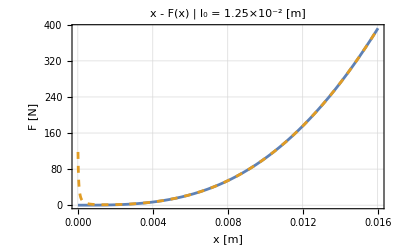
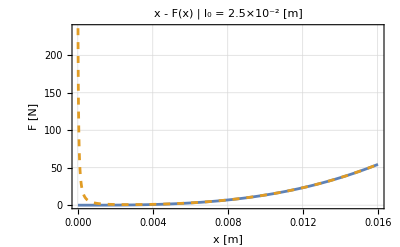
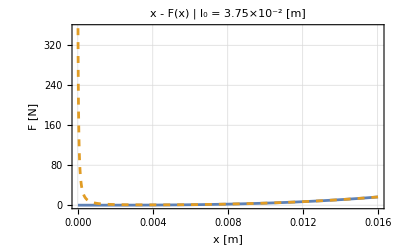

```mathematica
Row[
Flatten@Table[{
Plot[Evaluate@Table[Fpstrainl0[[i]]/.V->VV,{VV,{0,Vmaxl0[[i]]}}],{x,xmin,xmaxth},PlotStyle->{Automatic,Dashed},Evaluate@opts,PlotRangePadding->Scaled[0.01],PlotRange->All,FrameLabel->{"x [m]","F [N]"},PlotLabel->StringJoin["x - F(x) | ",l0strings[[i]]],ImageSize->400],Spacer@20},
{i,1,Length@l0range}]]
```

### Elastic energy from x - F

```mathematica
xrange=Range[xmin,0.5l0range,10^-5];
xrangenorm=xrange/l0range/.celldata;
```

```mathematica
Voll0=Vol//.pstrain/.{l0->l0range ,ξ0->ξ0range}/.celldata;
Volx=Table[Voll0[[i]]/.x->xrange[[i]],{i,1,Length@l0range}];
```

```mathematica
Uelx=Table[
ParallelTable[NIntegrate[(Fpstrainl0[[i]]/.V->Vmaxl0[[i]])-Fpstrainl0[[i]]/.V->0,{x,xmin,xfin}],{xfin,xrange[[i,1]],Last@xrange[[i]],GetStep@xrange[[i]]}],
{i,1,Length@l0range}];
```

```mathematica
uelx=Uelx/Volx/.celldata;
```

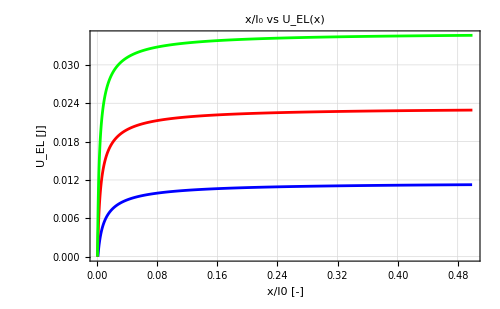
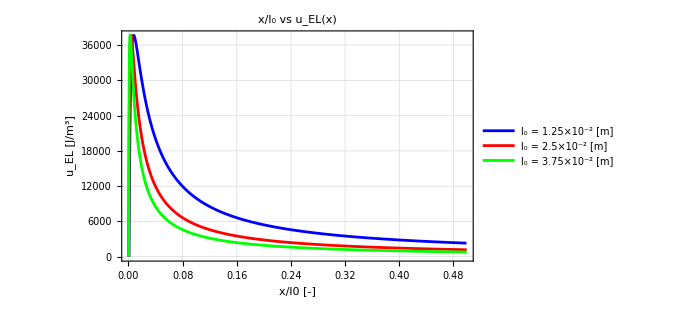

```mathematica
Row@{
Show[Table[
ListPlot[Transpose[{xrangenorm[[i]],Uelx[[i]]}],Joined->True,PlotStyle->colors[[i]]],{i,1,Length@l0range}],
PlotRange->All,Evaluate@opts,PlotLabel->"x/l_0 vs U_EL(x)",FrameLabel->{"x/l0 [-]","U_EL [J]"},ImageSize->500],Spacer@100,
Show[Table[
ListPlot[Transpose[{xrangenorm[[i]],uelx[[i]]}],PlotRange->All,Joined->True,PlotStyle->colors[[i]],PlotLegends->{l0strings[[i]]}],{i,1,Length@l0range}],
Evaluate@opts,PlotLabel->"x/l_0 vs u_EL(x)",FrameLabel->{"x/l0 [-]","u_EL [J/m^3]"},ImageSize->500]}
```

### Redefine x limits

```mathematica
xmax=0.3 l0/.l0->l0range/.celldata
```

{0.00375,0.0075,0.01125}

```mathematica
xrangeeff=Range[xmin,xmax,10^-5];
```

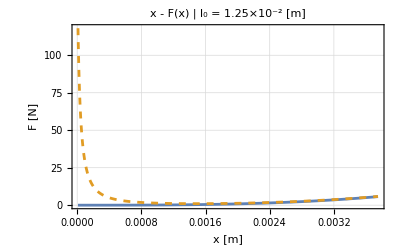
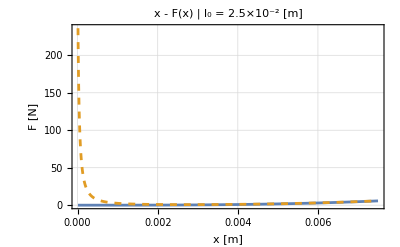
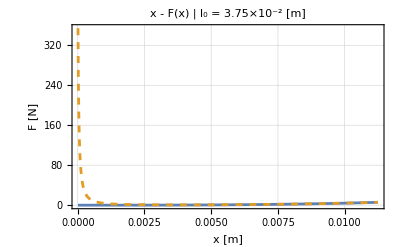

```mathematica
Row[
Flatten@Table[{
Plot[Evaluate@Table[Fpstrainl0[[i]]/.V->VV,{VV,{0,Vmaxl0[[i]]}}],{x,xmin,xmax[[i]]},PlotStyle->{Automatic,Dashed},Evaluate@opts,PlotRange->All,FrameLabel->{"x [m]","F [N]"},PlotLabel->StringJoin["x - F(x) | ",l0strings[[i]]],ImageSize->400],Spacer@20},
{i,1,Length@l0range}]]
```

### Q-V plots

```mathematica
Cvec=CC/.pstrain/.celldata/.x->xrange[[2]];
Vmaxvec=Vmax/.pstrain/.celldata/.x->xrange[[2]];
Qmaxvec=Cvec Vmaxvec;
```

```mathematica
VmaxofQQ=Interpolation[Transpose@{Qmaxvec,Vmaxvec}];
Qmaxlim=Flatten[VmaxofQQ["Domain"]][[2]]
QminlimVmax=Flatten[VmaxofQQ["Domain"]][[1]]
VmaxofQ[Q_]:=Piecewise[{{VmaxofQQ[Q], Between[Q,Flatten@VmaxofQQ["Domain"]]}, {-10^-50, Not@Between[1,Flatten@VmaxofQQ["Domain"]]}}]
```

7.51101×10^-6

1.68576×10^-7

Minimum strain -> C1 max, Maximum strain -> C1 min, C =Q/V, V  = Q/C, Q = C V

```mathematica
Cmin=CC/.pstrain/.celldata/.x->xmaxth
Cmax=CC/.pstrain/.celldata/.x->xmin
```

2.2707×10^-11

1.20182×10^-9

```mathematica
Vminstr[Q_]:=Q/Cmax;
Vmaxstr[Q_]:=Piecewise[{{Q/Cmin, Between[Q,{0,Flatten[VmaxofQQ["Domain"]][[1]]}]}, {-10^-50, Not@Between[Q,{0,Flatten[VmaxofQQ["Domain"]][[1]]}]}}];
```

```mathematica
Cminextr=(Flatten[VmaxofQQ["Domain"]][[1]])/VmaxofQ[Flatten[VmaxofQQ["Domain"]][[1]]]
```

2.73329×10^-11

```mathematica
VmaxofQ[Flatten[VmaxofQQ["Domain"]][[1]]]
```

6167.53

```mathematica
Cminextr-Cmin
```

4.6259×10^-12

```mathematica
Cmin
```

2.2707×10^-11

```mathematica
Vmaxstrextr[Q_]:=Piecewise[{{Q/Cminextr, Between[Q,{0,Flatten[VmaxofQQ["Domain"]][[1]]}]}, {-10^-50, Not@Between[Q,{0,Flatten[VmaxofQQ["Domain"]][[1]]}]}}];
```

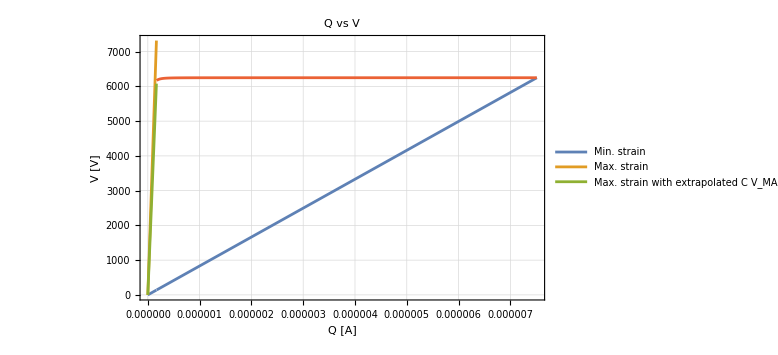

```mathematica
Plot[{Vminstr[Q],Vmaxstr[Q],Vmaxstrextr[Q],VmaxofQ[Q]},{Q,0,Qmaxlim},Evaluate@opts,PlotRange->{Automatic,{0,Automatic}},ImageSize->Large,FrameLabel->{"Q [A]","V [V]"},PlotLabel->"Q vs V",PlotLegends->{"Min. strain","Max. strain","Max. strain with extrapolated C""V_MAX"}]
```

```mathematica
VmaxofQ[Qmaxlim]==Vminstr/.Q->Qmaxlim
```

True

```mathematica
VmaxofQ[Flatten[VmaxofQQ["Domain"]][[1]]]==Vmaxstr[Flatten[VmaxofQQ["Domain"]][[1]]]
```

False

```mathematica
VmaxofQ[Flatten[VmaxofQQ["Domain"]][[1]]]==Vmaxstrextr[Flatten[VmaxofQQ["Domain"]][[1]]]
```

True

```mathematica
UelQV=ParallelTable[NIntegrate[Vmaxstrextr[Q]+VmaxofQ[Q]-Vminstr[Q],{Q,0,Qfin}],{Qfin,0,Qmaxlim,5 10^-8}];
```

```mathematica
LinSpace[xrangenorm[[2,1]],Last@xrangenorm[[2]],Length@UelQV]
```

{0.000400004,0.003728,0.007056,0.010384,0.013712,0.01704,0.020368,0.023696,0.027024,0.030352,0.03368,0.037008,0.040336,0.043664,0.046992,0.05032,0.053648,0.056976,0.060304,0.063632,0.06696,0.070288,0.073616,0.076944,0.080272,0.0836,0.086928,0.090256,0.093584,0.096912,0.10024,0.103568,0.106896,0.110224,0.113552,0.11688,0.120208,0.123536,0.126864,0.130192,0.13352,0.136848,0.140176,0.143504,0.146832,0.15016,0.153488,0.156816,0.160144,0.163472,0.1668,0.170128,0.173456,0.176784,0.180112,0.18344,0.186768,0.190096,0.193424,0.196752,0.20008,0.203408,0.206736,0.210064,0.213392,0.21672,0.220048,0.223376,0.226704,0.230032,0.23336,0.236688,0.240016,0.243344,0.246672,0.25,0.253328,0.256656,0.259984,0.263312,0.26664,0.269968,0.273296,0.276624,0.279952,0.28328,0.286608,0.289936,0.293264,0.296592,0.29992,0.303248,0.306576,0.309904,0.313232,0.31656,0.319888,0.323216,0.326544,0.329872,0.3332,0.336528,0.339856,0.343184,0.346512,0.34984,0.353168,0.356496,0.359824,0.363152,0.36648,0.369808,0.373136,0.376464,0.379792,0.38312,0.386448,0.389776,0.393104,0.396432,0.39976,0.403088,0.406416,0.409744,0.413072,0.4164,0.419728,0.423056,0.426384,0.429712,0.43304,0.436368,0.439696,0.443024,0.446352,0.44968,0.453008,0.456336,0.459664,0.462992,0.46632,0.469648,0.472976,0.476304,0.479632,0.48296,0.486288,0.489616,0.492944,0.496272,0.4996}

```mathematica
xofQ=Interpolation[Transpose@{(CC/.pstrain/.celldata)Vmax/.pstrain/.celldata/.x->xrange[[2]],xrange[[2]]},Q]
```

InterpolatingFunction[…][Q]

```mathematica
Qvectmp=LinSpace[QminlimVmax,Qmaxlim,Length@UelQV];
```

```mathematica
Table[xofQ[Qvectmp[[QQ]]],{QQ,1,Length@Qvectmp}]
```

{InterpolatingFunction[…][Q][1.68576×10^-7],InterpolatingFunction[…][Q][2.17526×10^-7],InterpolatingFunction[…][Q][2.66476×10^-7],InterpolatingFunction[…][Q][3.15425×10^-7],InterpolatingFunction[…][Q][3.64375×10^-7],InterpolatingFunction[…][Q][4.13324×10^-7],InterpolatingFunction[…][Q][4.62274×10^-7],InterpolatingFunction[…][Q][5.11223×10^-7],InterpolatingFunction[…][Q][5.60173×10^-7],InterpolatingFunction[…][Q][6.09123×10^-7],InterpolatingFunction[…][Q][6.58072×10^-7],InterpolatingFunction[…][Q][7.07022×10^-7],InterpolatingFunction[…][Q][7.55971×10^-7],InterpolatingFunction[…][Q][8.04921×10^-7],InterpolatingFunction[…][Q][8.5387×10^-7],InterpolatingFunction[…][Q][9.0282×10^-7],InterpolatingFunction[…][Q][9.5177×10^-7],InterpolatingFunction[…][Q][1.00072×10^-6],InterpolatingFunction[…][Q][1.04967×10^-6],InterpolatingFunction[…][Q][1.09862×10^-6],InterpolatingFunction[…][Q][1.14757×10^-6],InterpolatingFunction[…][Q][1.19652×10^-6],InterpolatingFunction[…][Q][1.24547×10^-6],InterpolatingFunction[…][Q][1.29442×10^-6],InterpolatingFunction[…][Q][1.34337×10^-6],InterpolatingFunction[…][Q][1.39232×10^-6],InterpolatingFunction[…][Q][1.44127×10^-6],InterpolatingFunction[…][Q][1.49021×10^-6],InterpolatingFunction[…][Q][1.53916×10^-6],InterpolatingFunction[…][Q][1.58811×10^-6],InterpolatingFunction[…][Q][1.63706×10^-6],InterpolatingFunction[…][Q][1.68601×10^-6],InterpolatingFunction[…][Q][1.73496×10^-6],InterpolatingFunction[…][Q][1.78391×10^-6],InterpolatingFunction[…][Q][1.83286×10^-6],InterpolatingFunction[…][Q][1.88181×10^-6],InterpolatingFunction[…][Q][1.93076×10^-6],InterpolatingFunction[…][Q][1.97971×10^-6],InterpolatingFunction[…][Q][2.02866×10^-6],InterpolatingFunction[…][Q][2.07761×10^-6],InterpolatingFunction[…][Q][2.12656×10^-6],InterpolatingFunction[…][Q][2.17551×10^-6],InterpolatingFunction[…][Q][2.22446×10^-6],InterpolatingFunction[…][Q][2.27341×10^-6],InterpolatingFunction[…][Q][2.32236×10^-6],InterpolatingFunction[…][Q][2.37131×10^-6],InterpolatingFunction[…][Q][2.42026×10^-6],InterpolatingFunction[…][Q][2.46921×10^-6],InterpolatingFunction[…][Q][2.51816×10^-6],InterpolatingFunction[…][Q][2.56711×10^-6],InterpolatingFunction[…][Q][2.61605×10^-6],InterpolatingFunction[…][Q][2.665×10^-6],InterpolatingFunction[…][Q][2.71395×10^-6],InterpolatingFunction[…][Q][2.7629×10^-6],InterpolatingFunction[…][Q][2.81185×10^-6],InterpolatingFunction[…][Q][2.8608×10^-6],InterpolatingFunction[…][Q][2.90975×10^-6],InterpolatingFunction[…][Q][2.9587×10^-6],InterpolatingFunction[…][Q][3.00765×10^-6],InterpolatingFunction[…][Q][3.0566×10^-6],InterpolatingFunction[…][Q][3.10555×10^-6],InterpolatingFunction[…][Q][3.1545×10^-6],InterpolatingFunction[…][Q][3.20345×10^-6],InterpolatingFunction[…][Q][3.2524×10^-6],InterpolatingFunction[…][Q][3.30135×10^-6],InterpolatingFunction[…][Q][3.3503×10^-6],InterpolatingFunction[…][Q][3.39925×10^-6],InterpolatingFunction[…][Q][3.4482×10^-6],InterpolatingFunction[…][Q][3.49715×10^-6],InterpolatingFunction[…][Q][3.5461×10^-6],InterpolatingFunction[…][Q][3.59505×10^-6],InterpolatingFunction[…][Q][3.644×10^-6],InterpolatingFunction[…][Q][3.69295×10^-6],InterpolatingFunction[…][Q][3.74189×10^-6],InterpolatingFunction[…][Q][3.79084×10^-6],InterpolatingFunction[…][Q][3.83979×10^-6],InterpolatingFunction[…][Q][3.88874×10^-6],InterpolatingFunction[…][Q][3.93769×10^-6],InterpolatingFunction[…][Q][3.98664×10^-6],InterpolatingFunction[…][Q][4.03559×10^-6],InterpolatingFunction[…][Q][4.08454×10^-6],InterpolatingFunction[…][Q][4.13349×10^-6],InterpolatingFunction[…][Q][4.18244×10^-6],InterpolatingFunction[…][Q][4.23139×10^-6],InterpolatingFunction[…][Q][4.28034×10^-6],InterpolatingFunction[…][Q][4.32929×10^-6],InterpolatingFunction[…][Q][4.37824×10^-6],InterpolatingFunction[…][Q][4.42719×10^-6],InterpolatingFunction[…][Q][4.47614×10^-6],InterpolatingFunction[…][Q][4.52509×10^-6],InterpolatingFunction[…][Q][4.57404×10^-6],InterpolatingFunction[…][Q][4.62299×10^-6],InterpolatingFunction[…][Q][4.67194×10^-6],InterpolatingFunction[…][Q][4.72089×10^-6],InterpolatingFunction[…][Q][4.76984×10^-6],InterpolatingFunction[…][Q][4.81879×10^-6],InterpolatingFunction[…][Q][4.86773×10^-6],InterpolatingFunction[…][Q][4.91668×10^-6],InterpolatingFunction[…][Q][4.96563×10^-6],InterpolatingFunction[…][Q][5.01458×10^-6],InterpolatingFunction[…][Q][5.06353×10^-6],InterpolatingFunction[…][Q][5.11248×10^-6],InterpolatingFunction[…][Q][5.16143×10^-6],InterpolatingFunction[…][Q][5.21038×10^-6],InterpolatingFunction[…][Q][5.25933×10^-6],InterpolatingFunction[…][Q][5.30828×10^-6],InterpolatingFunction[…][Q][5.35723×10^-6],InterpolatingFunction[…][Q][5.40618×10^-6],InterpolatingFunction[…][Q][5.45513×10^-6],InterpolatingFunction[…][Q][5.50408×10^-6],InterpolatingFunction[…][Q][5.55303×10^-6],InterpolatingFunction[…][Q][5.60198×10^-6],InterpolatingFunction[…][Q][5.65093×10^-6],InterpolatingFunction[…][Q][5.69988×10^-6],InterpolatingFunction[…][Q][5.74883×10^-6],InterpolatingFunction[…][Q][5.79778×10^-6],InterpolatingFunction[…][Q][5.84673×10^-6],InterpolatingFunction[…][Q][5.89568×10^-6],InterpolatingFunction[…][Q][5.94462×10^-6],InterpolatingFunction[…][Q][5.99357×10^-6],InterpolatingFunction[…][Q][6.04252×10^-6],InterpolatingFunction[…][Q][6.09147×10^-6],InterpolatingFunction[…][Q][6.14042×10^-6],InterpolatingFunction[…][Q][6.18937×10^-6],InterpolatingFunction[…][Q][6.23832×10^-6],InterpolatingFunction[…][Q][6.28727×10^-6],InterpolatingFunction[…][Q][6.33622×10^-6],InterpolatingFunction[…][Q][6.38517×10^-6],InterpolatingFunction[…][Q][6.43412×10^-6],InterpolatingFunction[…][Q][6.48307×10^-6],InterpolatingFunction[…][Q][6.53202×10^-6],InterpolatingFunction[…][Q][6.58097×10^-6],InterpolatingFunction[…][Q][6.62992×10^-6],InterpolatingFunction[…][Q][6.67887×10^-6],InterpolatingFunction[…][Q][6.72782×10^-6],InterpolatingFunction[…][Q][6.77677×10^-6],InterpolatingFunction[…][Q][6.82572×10^-6],InterpolatingFunction[…][Q][6.87467×10^-6],InterpolatingFunction[…][Q][6.92362×10^-6],InterpolatingFunction[…][Q][6.97257×10^-6],InterpolatingFunction[…][Q][7.02152×10^-6],InterpolatingFunction[…][Q][7.07046×10^-6],InterpolatingFunction[…][Q][7.11941×10^-6],InterpolatingFunction[…][Q][7.16836×10^-6],InterpolatingFunction[…][Q][7.21731×10^-6],InterpolatingFunction[…][Q][7.26626×10^-6],InterpolatingFunction[…][Q][7.31521×10^-6],InterpolatingFunction[…][Q][7.36416×10^-6],InterpolatingFunction[…][Q][7.41311×10^-6],InterpolatingFunction[…][Q][7.46206×10^-6],InterpolatingFunction[…][Q][7.51101×10^-6]}

```mathematica
Table[xofQ[],{QQ,Q}
```

```mathematica
NSolve[Q==(CC/.pstrain/.celldata)Vmax/.pstrain/.celldata ,x]
```

NSolve[Q==1/(0.00001-x)3.73342×10^-10 (1-0.428571 (-1+√(1+400. (-0.00001+x)^2))) √(1+400. (-0.00001+x)^2) (Log[0.025 (1.49565×10^-15-5.12036×10^-16 (-1+√(1+400. (-0.00001+x)^2)))]-Log[0.025 (1.19475×10^-15-5.12036×10^-16 (-1+√(1+400. (-0.00001+x)^2))+3.009×10^-11 x)]),x]

```mathematica
Vmax/.pstrain/.celldata
```

6249.71 (1-0.428571 (-1+√(1+400. (-0.00001+x)^2)))

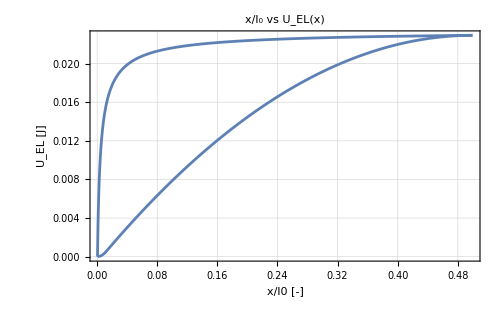

```mathematica
Show[
ListPlot[Transpose[{xrangenorm[[2]],Uelx[[2]]}],Joined->True],
ListPlot[Transpose[{LinSpace[xrangenorm[[2,1]],Last@xrangenorm[[2]],Length@UelQV],UelQV}],Joined->True],
PlotRange->All,Evaluate@opts,PlotLabel->"x/l_0 vs U_EL(x)",FrameLabel->{"x/l0 [-]","U_EL [J]"},ImageSize->500]
```

## Save

```mathematica
toexp=Association[
"tf"->tf,"l0range"->l0range,"w0range"->w0range,"tp0range"->tp0range,"ξ0range"->ξ0range,"xmin"->xmin,"xmaxth"->xmaxth,
"Vmax"->Vmax,
"PSTRAIN"->Association["pstraincond"->pstraincond,"geometry"->pstrain,"F"->Fpstrain,"xrange"->xrange,"Uelx"->Uelx[[2]],"uelx"->uelx[[2]]],
"PSTRESS"->Association["pstresscond"->pstresscond,"geometry"->pstress],
"NOSTRAIN"->Association["nostraincond"->nostraincond,"geometry"->nostrain]
];
```

```mathematica
Export["1DOF.m",toexp]
```

1DOF.m